## For the Sun Earth system

```mathematica
G=6.67408*10^(-11)
Ms=1.989*10^30
Me=5.972*10^24
d=1.496*10^11
X1=(Me*d)/(Ms+Me)
X2=(Ms*d)/(Ms+Me)
velocity=(G*(Ms+Me)/d)^(1/2)
period=(2*Pi*d)/velocity
thetadot=(2*Pi)/period
```

6.67408×10^-11

1.989×10^30

5.972×10^24

1.496×10^11

449175.

1.496×10^11

29788.5

3.15547×10^7

1.99121×10^-7

```mathematica
Solve[(-G*Ms)/((xs+X1)*Abs[xs+X1])-(G*Me)/((xs-X2)*Abs[xs-X2])+(thetadot)^(2)*xs==0,xs]
```

{{xs→-1.496×10^11},{xs→-1.496×10^11},{xs→1.48108×10^11},{xs→1.51101×10^11}}

```mathematica
TableForm[{{xs->-1.4960018715613318*^11},{xs->-1.496001122936799*^11},{xs->1.481081395922796*^11},{xs->1.5110094079765707*^11}}]
```

xs→-1.496×10^11
xs→-1.496×10^11
xs→1.48108×10^11
xs→1.51101×10^11

```mathematica
Lag1=1.481081395922796*^11
Lag2=1.5110094079765707*^11
Lag3=-1.496001122936799*^11
```

1.48108×10^11

1.51101×10^11

-1.496×10^11

```mathematica
Lag1Final=Lag1+X1
```

1.48109×10^11

```mathematica
Lag2Final=Lag2+X1
Lag3Final=Lag3+X1
```

1.51101×10^11

-1.496×10^11

```mathematica
Lag4Final = d
Lag5Fianl = d
```

1.496×10^11

1.496×10^11

These are distances to the Lagrange points form the center of the Sun in the Sun-Earth system.

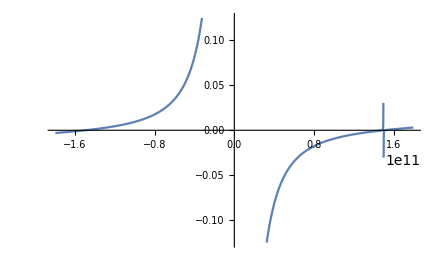

```mathematica
plot=Plot[(-G*Ms)/((xs+X1)*Abs[xs+X1])-(G*Me)/((xs-X2)*Abs[xs-X2])+(thetadot)^(2)*xs==0,{xs,-1.2*d,1.2*d}]
```

```mathematica
p1=Graphics[{PointSize[Large],Black,Point[{1.481081395922796*^11,0}]}]
p2=Graphics[{PointSize[Large],Red,Point[{1.5110094079765707*^11,0}]}]
p3=Graphics[{PointSize[Large],Green,Point[{-1.4959966311896017*^11,0}]}]
```

-Graphics-

-Graphics-

-Graphics-

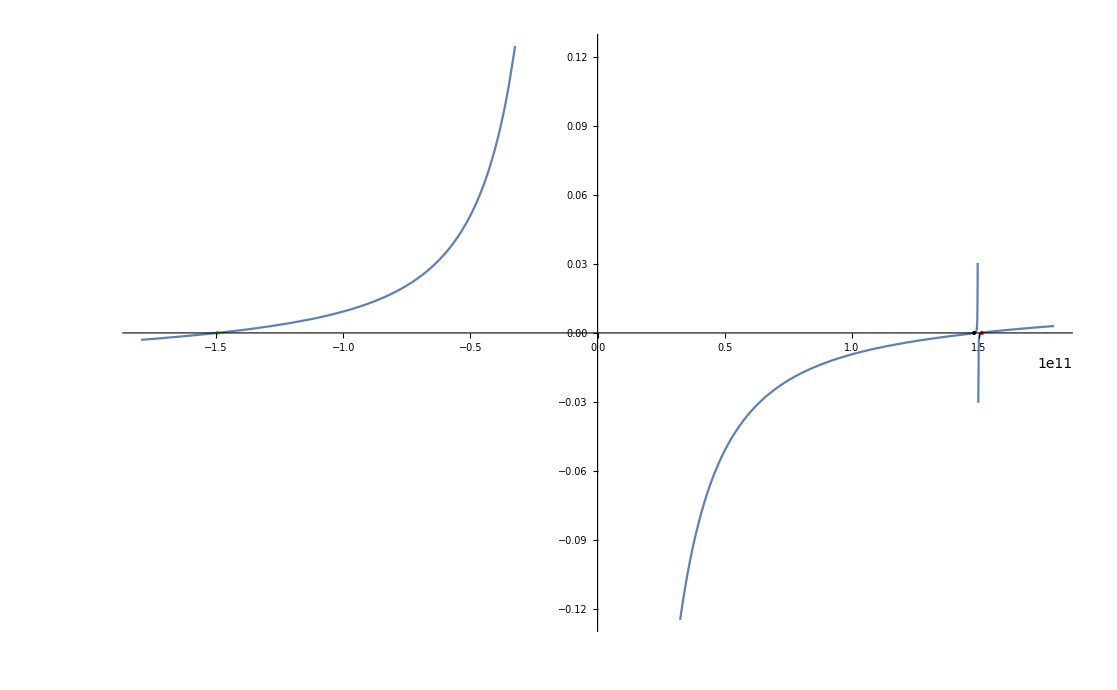

```mathematica
Show[plot,p1,p2,p3]
```

These are the solutions to the equation to find L1 (black), L2 (red) and L3 (green). They are the distances from the center of mass of the Sun-Earth system, which lies very close to the center of the sun, but not exactly. To get the points, one need only subtract the distance from the center of the coordinate system to the Sun, or the Earth. 


To get the distance from the Earth:

```mathematica
d
```

1.496×10^11

```mathematica
L1E=Lag1Final-d
```

-1.49141×10^9

```mathematica
L2E=Lag2Final-d
```

1.50139×10^9

```mathematica
L3E=Lag3Final-d
```

-2.992×10^11

These make sense because L1 would now be defined from Earth to the Lagrange point, thus pointing in the negative x-direction, L2 would be positive, and L3 would be almost/close to twice the distance between Earth and Sun. These are all in units of meters.

Found this really nice plot of the gravitational potential of the two-body gravitational system. (Not my own work)
https://demonstrations.wolfram.com/LagrangePoints/

```mathematica
potential[x_,y_,a_,ξ1_]:=1/2 (-x^2/a^2-y^2/a^2)+(-1+ξ1)/(√(y^2/a^2+(x/a-ξ1)^2))-ξ1/(√(y^2/a^2+(1+x/a-ξ1)^2))
```

```mathematica
Manipulate[ Module[{sols,deriv,posAtL1,posAtL2,posAtL3,posAtL4,posAtL5}, deriv=D[potential[x,0,a,ξ1],x]; posAtL1=FindRoot[deriv==0,{x,0}]; posAtL2=FindRoot[deriv==0,{x,1.5}]; posAtL3=FindRoot[deriv==0,{x,-1}];posAtL4=FindRoot[{D[potential[x,y,a,ξ1], x]==0,D[potential[x,y,a,ξ1], y]==0},{{x,0},{y,1}}]; posAtL5=FindRoot[{D[potential[x,y,a,ξ1], x]==0,D[potential[x,y,a,ξ1], y]==0},{{x,0},{y,-1}}]; sols={{x/.posAtL1,0,potential[x/.posAtL1,0,a,ξ1]},{x/.posAtL2,0,potential[x/.posAtL2,0,a,ξ1]},{x/.posAtL3,0,potential[x/.posAtL3,0,a,ξ1]},{x/.posAtL4,y/.posAtL4,potential[x/.posAtL4,y/.posAtL4,a,ξ1]},{x/.posAtL5,y/.posAtL5,potential[x/.posAtL5,y/.posAtL5,a,ξ1]}}; If[view=="2D",ContourPlot[potential[x,y,a,ξ1],{x,-3/2,3/2},{y,-3/2,3/2},ContourStyle->{Dashed},MaxRecursion->ControlActive[1,Automatic],ColorFunction->"Rainbow",Frame->False,Epilog->{PointSize[.015],Point[Most[#]&/@sols]},ImageSize->{350,350},Axes->False],Show[Plot3D[potential[x,y,a,ξ1],{x,-3,3},{y,-3,3},PlotStyle->{Opacity[.5]},ColorFunction->"Rainbow",MeshShading->{None, Automatic},MeshFunctions -> {#3&}],Graphics3D@{PointSize[.02],Point[sols]},ImageSize->{350,350}]]], {{a,1,"distance between masses"},0.2,1.2}, {{ξ1,1/3.,"mass ratio"},.2,.75}, {view,{"2D","3D"}},AutorunSequencing->{2},SaveDefinitions->True,TrackedSymbols:>Manipulate,SynchronousUpdating->False]
```

The 3 D model shows how the rotation of the system causes the centrifugal force. This force acts from the center of the system outwards, and can thus be illustrated by making the gravitational potential surface a curved surface.